```mathematica
Clear[ girl, boy ] ;
boy = Import[ "http://imgur.com/mRRhOgo.jpg" ]
girl = Import[ "http://imgur.com/Q5ReXSX.jpg" ]
```

-Graphics-

-Graphics-

```mathematica
justGray[image_] := Module[{imageP, image2},
imageP=ColorNegate@ImageAdjust@ImageDifference[image,(ColorSeparate@image)[[3]]];
image2=ColorNegate@ImageAdjust@ImageSubtract[imageP,image];
 Binarize[(ColorSeparate@image2)[[1]],0.8]
]

girlBW = justGray[ girl] 
boyBW = justGray[ boy ]
```

-Graphics-

-Graphics-

{RGBColor[0.972232,0.972529,0.971961],RGBColor[0.835386,0.786578,0.794398],RGBColor[0.842429,0.633388,0.727112],RGBColor[0.878478,0.926024,0.93836],RGBColor[0.799081,0.90285,0.929044]}

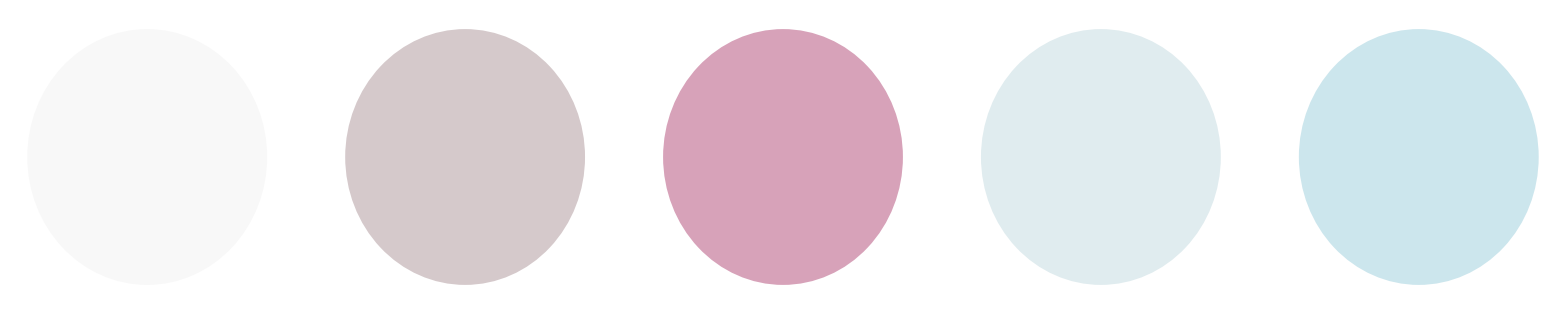
-Graphics-
-Graphics-

-Graphics-

$Aborted

```mathematica
newspace[{r_,g_,b_}]:={r-g,b-g,(r+g+b)/10}
rgbspace[{x_,y_,z_}]:={(2 x-y+10 z)/3,(-x-y+10 z)/3,(-x+2 y+10 z)/3}

dominants[image_,n_]:=Module[{data,cols},data=Flatten[ImageData[image],1];
data=newspace/@data;
cols=Mean/@FindClusters[data,n];
RGBColor@@@rgbspace/@cols]

image=girl~ImageResize~150;
d = dominants[image,5]
Column[{image,GraphicsRow[Graphics[{#,Disk[]}]&/@d]}]

colorExpose[im_,col_,tol_: .005]:=Module[{color=Apply[List,ColorConvert[col,"RGB"]],r=If[ImageColorSpace[im]≠"RGB",ColorConvert[im,"RGB"],im]},SetAlphaChannel[r,Binarize[r,(Norm[#-color]<tol)&]]]

(*ra=Import["http://i.stack.imgur.com/zzUdB.gif"]*)
colorExpose[ColorConvert[girl,"CMYK"],RGBColor[0.8353856575309894,0.7865784222185629,0.7943977591036436]]
colorExpose[girl,Hue[.5]]
```

```mathematica
? ColorSeparate
```

ColorSeparate[image] gives a list of single-channel images corresponding to each of the color channels in image.
ColorSeparate[image,colorspace] gives a list of images corresponding to the components of colorspace.